First Values

First Values

```mathematica
ClearAll[θ,a,l,ω,t];
l=0.5;
V=1;θo=Pi;ω=18Pi;a=0.5;t0=9;g=9.8;L=(1/2 l^2) θ'[t]^2+((((a l) ω) Sin[ω t]) Sin[θ[t]]) θ'[t]+((1/2 a^2) ω^2) Sin[ω t]^2+g (l Cos[θ[t]]+a Cos[ω t]);EoM={D[L, θ[t]]-D[D[L, θ'[t]], t]==0,θ[0]==θo,θ'[0]==V};sol1=NDSolve[EoM,θ,{t,0,t0}];
```

θ 1values

values θ

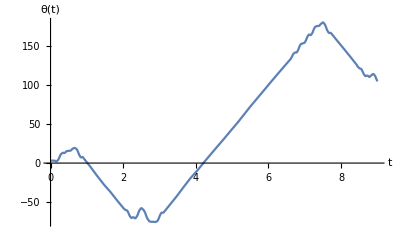

```mathematica
Table[Evaluate[θ[t]/.sol1],{t,0,t0,0.1}];
Plot[Evaluate[θ[t]/.sol1],{t,0,t0},PlotRange->All,AxesLabel->{t,θ[t]}]
```

x 1values

values x

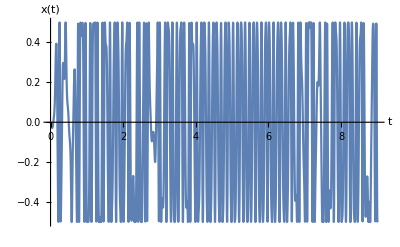

```mathematica
Table[l Sin[θ[t]/.sol1],{t,0,t0,0.1}];
Plot[l Sin[θ[t]/.sol1],{t,0,t0},PlotRange->All,AxesLabel->{t,x[t]}]
```

y1values

y1values

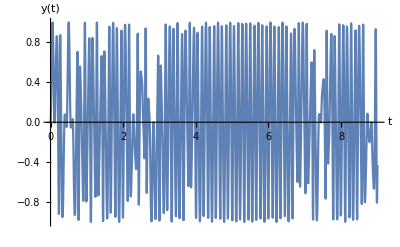

```mathematica
Table[-l Cos[θ[t]/.sol1]-a Cos[ω t],{t,0,t0,0.1}];
Plot[-l Cos[θ[t]/.sol1]-a Cos[ω t],{t,0,t0},PlotRange->All,AxesLabel->{t,y[t]}]
```

Second values

Second values

```mathematica
ClearAll[α,b,l,ω,t];
l=0.5;
V=1;αo=Pi;ω=18Pi;b=0.50001;t0=9;g=9.8;Lagrangian=(1/2 l^2) α'[t]^2+((((b l) ω) Sin[ω t]) Sin[α[t]]) α'[t]+((1/2 b^2) ω^2) Sin[ω t]^2+g (l Cos[α[t]]+b Cos[ω t]);EOM={D[Lagrangian, α[t]]-D[D[Lagrangian, α'[t]], t]==0,α[0]==αo,α'[0]==V};sol2=NDSolve[EOM,α,{t,0,t0}];
```

θ2 values

values θ2

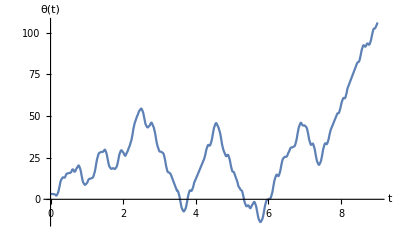

```mathematica
Table[Evaluate[α[t]/.sol2],{t,0,t0,0.1}];
Plot[Evaluate[α[t]/.sol2],{t,0,t0},PlotRange->All,AxesLabel->{t,θ[t]}]
```

x 2values

2 values x

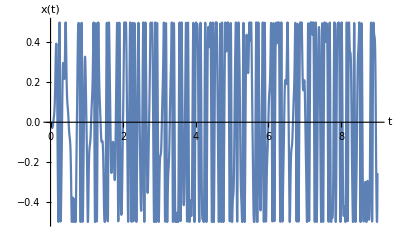

```mathematica
Table[l Sin[α[t]/.sol2],{t,0,t0,0.1}];
Plot[l Sin[α[t]/.sol2],{t,0,t0},PlotRange->All,AxesLabel->{t,x[t]}]
```

y2 Values

Values y2

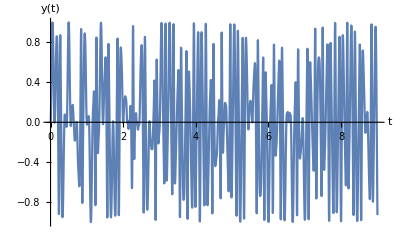

```mathematica
Table[-l Cos[α[t]/.sol2]-b Cos[ω t],{t,0,t0,0.1}];
Plot[-l Cos[α[t]/.sol2]-b Cos[ω t],{t,0,t0},PlotRange->All,AxesLabel->{t,y[t]}]
```

θ  Divergence

Divergence θ

```mathematica
T=(Log[Abs[(Evaluate[α[t]/.sol2]-Evaluate[θ[t]/.sol1]+0.00001)]]);
```

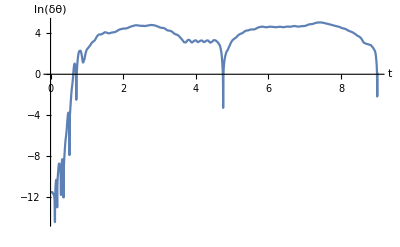

```mathematica
{Table[T,{t,0,t0,0.1}],{t,0,t0,0.1}};
Plot[T,{t,0,t0},PlotRange->All,AxesLabel->{t,ln[δθ]}]
```

y  Divergence

Divergence y

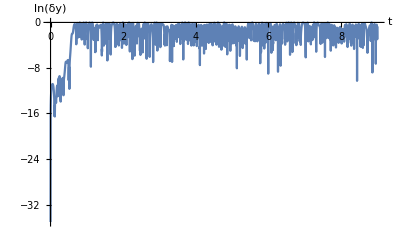

```mathematica
Y=Log[Abs[(-l Cos[α[t]/.sol2]-b Cos[ω t]+l Cos[θ[t]/.sol1]+a Cos[ω t])+0.00001]];
Plot[Y,{t,0,t0},PlotRange->All,AxesLabel->{t,ln[δy]}]
```

x  Divergence

Divergence x

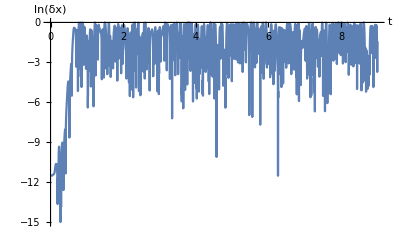

```mathematica
X=Log[Abs[(l Sin[α[t]/.sol2]-l Sin[θ[t]/.sol1])+0.00001]];
Plot[X,{t,0,t0},PlotRange->All,AxesLabel->{t,ln[δx]}]
```